## Practice

```mathematica
Clear[$PrePrint]
```

```mathematica
f=FunctionInterpolation[-3 x^2+4,{x,-3,3 }]
```

InterpolatingFunction[…]

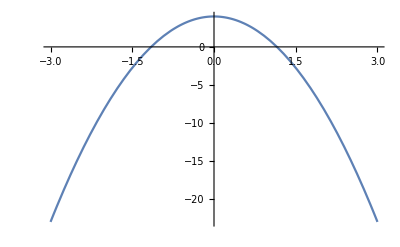

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
Solve[-3 x^2+4==0]
```

{{x→-2/(√3)},{x→2/(√3)}}

```mathematica
FInt=Integrate[f[x],x]
```

InterpolatingFunction[…](x)

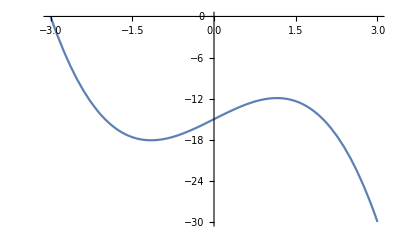

```mathematica
Plot[%,{x,-3,3}]
```

```mathematica
FDev=D[f[x],x]
```

InterpolatingFunction[…](x)

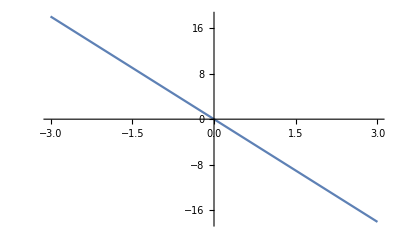

```mathematica
Plot[%,{x,-3,3}]
```

## Compare to Duhr Paper, (Npt = 10), 100 GeV < Mass < 700 GeV

```mathematica
data = Import["~/Desktop/LegendreIntegration.dat"]
```

{{100.,0.0000342197,2.89599,0.000204082,0.0000118162,389.379},{160.,0.0000125257,1.69607,0.000522449,7.38515×10^-6,95.0633},{220.,6.02184×10^-6,1.12117,0.000987755,5.37102×10^-6,36.5683},{280.,3.34542×10^-6,0.792738,0.0016,4.22009×10^-6,17.7378},{340.,2.03246×10^-6,0.584819,0.00235918,3.47537×10^-6,9.90686},{400.,1.31182×10^-6,0.444073,0.00326531,2.95406×10^-6,6.08405},{460.,8.84276×10^-7,0.344244,0.00431837,2.56875×10^-6,4.00036},{520.,6.15776×10^-7,0.270986,0.00551837,2.27235×10^-6,2.76925},{580.,4.39712×10^-7,0.215833,0.00686531,2.03728×10^-6,1.99567},{640.,3.20299×10^-7,0.173482,0.00835918,1.84629×10^-6,1.48536},{700.,2.37095×10^-7,0.140456,0.01,1.68804×10^-6,1.13522}}

```mathematica
TableForm[data]
Mass = data[[All,1]]
dσDM = data[[All,2]]
```

100. | 0.0000342197 | 2.89599 | 0.000204082 | 0.0000118162 | 389.379
160. | 0.0000125257 | 1.69607 | 0.000522449 | 7.38515×10^-6 | 95.0633
220. | 6.02184×10^-6 | 1.12117 | 0.000987755 | 5.37102×10^-6 | 36.5683
280. | 3.34542×10^-6 | 0.792738 | 0.0016 | 4.22009×10^-6 | 17.7378
340. | 2.03246×10^-6 | 0.584819 | 0.00235918 | 3.47537×10^-6 | 9.90686
400. | 1.31182×10^-6 | 0.444073 | 0.00326531 | 2.95406×10^-6 | 6.08405
460. | 8.84276×10^-7 | 0.344244 | 0.00431837 | 2.56875×10^-6 | 4.00036
520. | 6.15776×10^-7 | 0.270986 | 0.00551837 | 2.27235×10^-6 | 2.76925
580. | 4.39712×10^-7 | 0.215833 | 0.00686531 | 2.03728×10^-6 | 1.99567
640. | 3.20299×10^-7 | 0.173482 | 0.00835918 | 1.84629×10^-6 | 1.48536
700. | 2.37095×10^-7 | 0.140456 | 0.01 | 1.68804×10^-6 | 1.13522

{100.,160.,220.,280.,340.,400.,460.,520.,580.,640.,700.}

{0.0000342197,0.0000125257,6.02184×10^-6,3.34542×10^-6,2.03246×10^-6,1.31182×10^-6,8.84276×10^-7,6.15776×10^-7,4.39712×10^-7,3.20299×10^-7,2.37095×10^-7}

```mathematica
data1 = Import["~/Desktop/LegendreIntegration2.dat"]
TableForm[data1]
Mass1 = data1[[All,1]]
dσDM1 = data1[[All,2]]
```

(100. | 0.0000342197 | 2.89599 | 0.000204082 | 0.0000118162 | 389.379
160. | 0.0000125257 | 1.69607 | 0.000522449 | 7.38515×10^-6 | 95.0633
220. | 6.02184×10^-6 | 1.12117 | 0.000987755 | 5.37102×10^-6 | 36.5683
280. | 3.34542×10^-6 | 0.792738 | 0.0016 | 4.22009×10^-6 | 17.7378
340. | 2.03246×10^-6 | 0.584819 | 0.00235918 | 3.47537×10^-6 | 9.90686
400. | 1.31182×10^-6 | 0.444073 | 0.00326531 | 2.95406×10^-6 | 6.08405
460. | 8.84276×10^-7 | 0.344244 | 0.00431837 | 2.56875×10^-6 | 4.00036
520. | 6.15776×10^-7 | 0.270986 | 0.00551837 | 2.27235×10^-6 | 2.76925
580. | 4.39712×10^-7 | 0.215833 | 0.00686531 | 2.03728×10^-6 | 1.99567
640. | 3.20299×10^-7 | 0.173482 | 0.00835918 | 1.84629×10^-6 | 1.48536
700. | 2.37095×10^-7 | 0.140456 | 0.01 | 1.68804×10^-6 | 1.13522)

100. | 0.0000342197 | 2.89599 | 0.000204082 | 0.0000118162 | 389.379
160. | 0.0000125257 | 1.69607 | 0.000522449 | 7.38515×10^-6 | 95.0633
220. | 6.02184×10^-6 | 1.12117 | 0.000987755 | 5.37102×10^-6 | 36.5683
280. | 3.34542×10^-6 | 0.792738 | 0.0016 | 4.22009×10^-6 | 17.7378
340. | 2.03246×10^-6 | 0.584819 | 0.00235918 | 3.47537×10^-6 | 9.90686
400. | 1.31182×10^-6 | 0.444073 | 0.00326531 | 2.95406×10^-6 | 6.08405
460. | 8.84276×10^-7 | 0.344244 | 0.00431837 | 2.56875×10^-6 | 4.00036
520. | 6.15776×10^-7 | 0.270986 | 0.00551837 | 2.27235×10^-6 | 2.76925
580. | 4.39712×10^-7 | 0.215833 | 0.00686531 | 2.03728×10^-6 | 1.99567
640. | 3.20299×10^-7 | 0.173482 | 0.00835918 | 1.84629×10^-6 | 1.48536
700. | 2.37095×10^-7 | 0.140456 | 0.01 | 1.68804×10^-6 | 1.13522

{100.,160.,220.,280.,340.,400.,460.,520.,580.,640.,700.}

{0.0000342197,0.0000125257,6.02184×10^-6,3.34542×10^-6,2.03246×10^-6,1.31182×10^-6,8.84276×10^-7,6.15776×10^-7,4.39712×10^-7,3.20299×10^-7,2.37095×10^-7}

```mathematica
fint = Interpolation[Transpose[{Col1,Col2}],InterpolationOrder->3]
```

InterpolatingFunction[…]

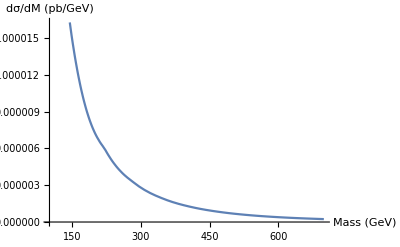

```mathematica
Plot[fint[x],{x,100,700},AxesLabel->{"Mass (GeV)","dσ/dM (pb/GeV)"}]
```

```mathematica
F1=Integrate[f1[x],x]
```

InterpolatingFunction[…][x]

InterpolatingFunction::dmval: Input value {50.0133} lies outside the range of data in the interpolating function. Extrapolation will be used.

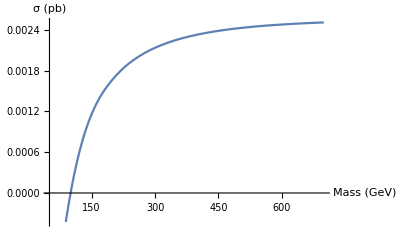

```mathematica
Plot[F1,{x,50,700},AxesLabel->{"Mass (GeV)","σ (pb)"}]
```

## Compare to Duhr Paper, (Npt = 50), 10 GeV < Mass < 2000 GeV

```mathematica
Clear[data]
```

```mathematica
data = Import["~/Desktop/LegendreIntegration.dat"]
```

{{10.,0.000665169,19.4152,5.91716×10^-7,0.0000342601,389379.},{49.8,0.0000697393,10.1372,0.0000146748,6.87954×10^-6,3152.72},{89.6,0.0000243593,6.37066,0.0000475039,3.82367×10^-6,541.314},{129.4,0.0000119227,4.50319,0.0000990791,2.64761×10^-6,179.709},{169.2,6.88852×10^-6,3.40202,0.0001694,2.02483×10^-6,80.3844},{209.,4.39727×10^-6,2.6825,0.000258467,1.63924×10^-6,42.6515},{248.8,3.00106×10^-6,2.1794,0.000366281,1.37701×10^-6,25.2826},{288.6,2.14895×10^-6,1.81023,0.00049284,1.18711×10^-6,16.1988},{328.4,1.59554×10^-6,1.5294,0.000638145,1.04324×10^-6,10.9942},{368.2,1.21863×10^-6,1.30968,0.000802197,9.30476×10^-7,7.80048},{408.,9.52111×10^-7,1.13386,0.000984994,8.39709×10^-7,5.73314},{447.8,7.57851×10^-7,0.990556,0.00118654,7.65076×10^-7,4.33631},{487.6,6.1266×10^-7,0.871956,0.00140683,7.02628×10^-7,3.35878},{527.4,5.01832×10^-7,0.77252,0.00164586,6.49604×10^-7,2.65432},{567.2,4.15701×10^-7,0.688222,0.00190364,6.04022×10^-7,2.13385},{607.,3.47722×10^-7,0.616073,0.00218017,5.64417×10^-7,1.74103},{646.8,2.93343×10^-7,0.553805,0.00247545,5.29686×10^-7,1.43901},{686.6,2.49327×10^-7,0.49967,0.00278946,4.98982×10^-7,1.20299},{726.4,2.13325×10^-7,0.452302,0.00312223,4.71643×10^-7,1.01589},{766.2,1.83604×10^-7,0.410615,0.00347374,4.47143×10^-7,0.865658},{806.,1.58863×10^-7,0.373739,0.003844,4.25064×10^-7,0.743649},{845.8,1.38114×10^-7,0.34097,0.004233,4.05062×10^-7,0.643532},{885.6,1.20595×10^-7,0.311729,0.00464075,3.86858×10^-7,0.560609},{925.4,1.05712×10^-7,0.28554,0.00506725,3.7022×10^-7,0.491343},{965.2,9.29987×10^-8,0.262003,0.00551249,3.54954×10^-7,0.433033},{1005.,8.20826×10^-8,0.240784,0.00597648,3.40897×10^-7,0.383597},{1044.8,7.26661×10^-8,0.221603,0.00645921,3.27911×10^-7,0.341408},{1084.6,6.45081×10^-8,0.204218,0.00696069,3.15878×10^-7,0.305186},{1124.4,5.74124×10^-8,0.188425,0.00748092,3.04697×10^-7,0.273912},{1164.2,5.12182×10^-8,0.174046,0.00801989,2.9428×10^-7,0.246769},{1204.,4.57926×10^-8,0.160928,0.00857761,2.84552×10^-7,0.223097},{1243.8,4.10252×10^-8,0.14894,0.00915407,2.75447×10^-7,0.202358},{1283.6,3.68239×10^-8,0.137966,0.00974928,2.66907×10^-7,0.184113},{1323.4,3.31115×10^-8,0.127903,0.0103632,2.5888×10^-7,0.167996},{1363.2,2.98226×10^-8,0.118663,0.0109959,2.51321×10^-7,0.153707},{1403.,2.6902×10^-8,0.110167,0.0116474,2.44192×10^-7,0.140994},{1442.8,2.43027×10^-8,0.102346,0.0123176,2.37456×10^-7,0.129645},{1482.6,2.19845×10^-8,0.0951375,0.0130065,2.31081×10^-7,0.119482},{1522.4,1.99129×10^-8,0.0884861,0.0137142,2.2504×10^-7,0.110354},{1562.2,1.80583×10^-8,0.0823427,0.0144406,2.19307×10^-7,0.102132},{1602.,1.63951×10^-8,0.0766632,0.0151858,2.13858×10^-7,0.0947077},{1641.8,1.4901×10^-8,0.0714078,0.0159497,2.08674×10^-7,0.0879857},{1681.6,1.35567×10^-8,0.066541,0.0167324,2.03735×10^-7,0.0818851},{1721.4,1.23456×10^-8,0.0620304,0.0175338,1.99025×10^-7,0.0763357},{1761.2,1.12528×10^-8,0.057847,0.018354,1.94527×10^-7,0.0712766},{1801.,1.02656×10^-8,0.0539644,0.0191929,1.90228×10^-7,0.0666549},{1840.8,9.37252×10^-9,0.0503587,0.0200506,1.86115×10^-7,0.0624242},{1880.6,8.56376×10^-9,0.047008,0.020927,1.82177×10^-7,0.0585442},{1920.4,7.83051×10^-9,0.0438927,0.0218221,1.78401×10^-7,0.0549791},{1960.2,7.165×10^-9,0.0409947,0.022736,1.74779×10^-7,0.0516978},{2000.,6.56036×10^-9,0.0382974,0.0236686,1.71301×10^-7,0.0486724}}

```mathematica
TableForm[data]
Mass = data[[All,1]]
dσdM = data[[All,2]]
```

10. | 0.000665169 | 19.4152 | 5.91716×10^-7 | 0.0000342601 | 389379.
49.8 | 0.0000697393 | 10.1372 | 0.0000146748 | 6.87954×10^-6 | 3152.72
89.6 | 0.0000243593 | 6.37066 | 0.0000475039 | 3.82367×10^-6 | 541.314
129.4 | 0.0000119227 | 4.50319 | 0.0000990791 | 2.64761×10^-6 | 179.709
169.2 | 6.88852×10^-6 | 3.40202 | 0.0001694 | 2.02483×10^-6 | 80.3844
209. | 4.39727×10^-6 | 2.6825 | 0.000258467 | 1.63924×10^-6 | 42.6515
248.8 | 3.00106×10^-6 | 2.1794 | 0.000366281 | 1.37701×10^-6 | 25.2826
288.6 | 2.14895×10^-6 | 1.81023 | 0.00049284 | 1.18711×10^-6 | 16.1988
328.4 | 1.59554×10^-6 | 1.5294 | 0.000638145 | 1.04324×10^-6 | 10.9942
368.2 | 1.21863×10^-6 | 1.30968 | 0.000802197 | 9.30476×10^-7 | 7.80048
408. | 9.52111×10^-7 | 1.13386 | 0.000984994 | 8.39709×10^-7 | 5.73314
447.8 | 7.57851×10^-7 | 0.990556 | 0.00118654 | 7.65076×10^-7 | 4.33631
487.6 | 6.1266×10^-7 | 0.871956 | 0.00140683 | 7.02628×10^-7 | 3.35878
527.4 | 5.01832×10^-7 | 0.77252 | 0.00164586 | 6.49604×10^-7 | 2.65432
567.2 | 4.15701×10^-7 | 0.688222 | 0.00190364 | 6.04022×10^-7 | 2.13385
607. | 3.47722×10^-7 | 0.616073 | 0.00218017 | 5.64417×10^-7 | 1.74103
646.8 | 2.93343×10^-7 | 0.553805 | 0.00247545 | 5.29686×10^-7 | 1.43901
686.6 | 2.49327×10^-7 | 0.49967 | 0.00278946 | 4.98982×10^-7 | 1.20299
726.4 | 2.13325×10^-7 | 0.452302 | 0.00312223 | 4.71643×10^-7 | 1.01589
766.2 | 1.83604×10^-7 | 0.410615 | 0.00347374 | 4.47143×10^-7 | 0.865658
806. | 1.58863×10^-7 | 0.373739 | 0.003844 | 4.25064×10^-7 | 0.743649
845.8 | 1.38114×10^-7 | 0.34097 | 0.004233 | 4.05062×10^-7 | 0.643532
885.6 | 1.20595×10^-7 | 0.311729 | 0.00464075 | 3.86858×10^-7 | 0.560609
925.4 | 1.05712×10^-7 | 0.28554 | 0.00506725 | 3.7022×10^-7 | 0.491343
965.2 | 9.29987×10^-8 | 0.262003 | 0.00551249 | 3.54954×10^-7 | 0.433033
1005. | 8.20826×10^-8 | 0.240784 | 0.00597648 | 3.40897×10^-7 | 0.383597
1044.8 | 7.26661×10^-8 | 0.221603 | 0.00645921 | 3.27911×10^-7 | 0.341408
1084.6 | 6.45081×10^-8 | 0.204218 | 0.00696069 | 3.15878×10^-7 | 0.305186
1124.4 | 5.74124×10^-8 | 0.188425 | 0.00748092 | 3.04697×10^-7 | 0.273912
1164.2 | 5.12182×10^-8 | 0.174046 | 0.00801989 | 2.9428×10^-7 | 0.246769
1204. | 4.57926×10^-8 | 0.160928 | 0.00857761 | 2.84552×10^-7 | 0.223097
1243.8 | 4.10252×10^-8 | 0.14894 | 0.00915407 | 2.75447×10^-7 | 0.202358
1283.6 | 3.68239×10^-8 | 0.137966 | 0.00974928 | 2.66907×10^-7 | 0.184113
1323.4 | 3.31115×10^-8 | 0.127903 | 0.0103632 | 2.5888×10^-7 | 0.167996
1363.2 | 2.98226×10^-8 | 0.118663 | 0.0109959 | 2.51321×10^-7 | 0.153707
1403. | 2.6902×10^-8 | 0.110167 | 0.0116474 | 2.44192×10^-7 | 0.140994
1442.8 | 2.43027×10^-8 | 0.102346 | 0.0123176 | 2.37456×10^-7 | 0.129645
1482.6 | 2.19845×10^-8 | 0.0951375 | 0.0130065 | 2.31081×10^-7 | 0.119482
1522.4 | 1.99129×10^-8 | 0.0884861 | 0.0137142 | 2.2504×10^-7 | 0.110354
1562.2 | 1.80583×10^-8 | 0.0823427 | 0.0144406 | 2.19307×10^-7 | 0.102132
1602. | 1.63951×10^-8 | 0.0766632 | 0.0151858 | 2.13858×10^-7 | 0.0947077
1641.8 | 1.4901×10^-8 | 0.0714078 | 0.0159497 | 2.08674×10^-7 | 0.0879857
1681.6 | 1.35567×10^-8 | 0.066541 | 0.0167324 | 2.03735×10^-7 | 0.0818851
1721.4 | 1.23456×10^-8 | 0.0620304 | 0.0175338 | 1.99025×10^-7 | 0.0763357
1761.2 | 1.12528×10^-8 | 0.057847 | 0.018354 | 1.94527×10^-7 | 0.0712766
1801. | 1.02656×10^-8 | 0.0539644 | 0.0191929 | 1.90228×10^-7 | 0.0666549
1840.8 | 9.37252×10^-9 | 0.0503587 | 0.0200506 | 1.86115×10^-7 | 0.0624242
1880.6 | 8.56376×10^-9 | 0.047008 | 0.020927 | 1.82177×10^-7 | 0.0585442
1920.4 | 7.83051×10^-9 | 0.0438927 | 0.0218221 | 1.78401×10^-7 | 0.0549791
1960.2 | 7.165×10^-9 | 0.0409947 | 0.022736 | 1.74779×10^-7 | 0.0516978
2000. | 6.56036×10^-9 | 0.0382974 | 0.0236686 | 1.71301×10^-7 | 0.0486724

{10.,49.8,89.6,129.4,169.2,209.,248.8,288.6,328.4,368.2,408.,447.8,487.6,527.4,567.2,607.,646.8,686.6,726.4,766.2,806.,845.8,885.6,925.4,965.2,1005.,1044.8,1084.6,1124.4,1164.2,1204.,1243.8,1283.6,1323.4,1363.2,1403.,1442.8,1482.6,1522.4,1562.2,1602.,1641.8,1681.6,1721.4,1761.2,1801.,1840.8,1880.6,1920.4,1960.2,2000.}

{0.000665169,0.0000697393,0.0000243593,0.0000119227,6.88852×10^-6,4.39727×10^-6,3.00106×10^-6,2.14895×10^-6,1.59554×10^-6,1.21863×10^-6,9.52111×10^-7,7.57851×10^-7,6.1266×10^-7,5.01832×10^-7,4.15701×10^-7,3.47722×10^-7,2.93343×10^-7,2.49327×10^-7,2.13325×10^-7,1.83604×10^-7,1.58863×10^-7,1.38114×10^-7,1.20595×10^-7,1.05712×10^-7,9.29987×10^-8,8.20826×10^-8,7.26661×10^-8,6.45081×10^-8,5.74124×10^-8,5.12182×10^-8,4.57926×10^-8,4.10252×10^-8,3.68239×10^-8,3.31115×10^-8,2.98226×10^-8,2.6902×10^-8,2.43027×10^-8,2.19845×10^-8,1.99129×10^-8,1.80583×10^-8,1.63951×10^-8,1.4901×10^-8,1.35567×10^-8,1.23456×10^-8,1.12528×10^-8,1.02656×10^-8,9.37252×10^-9,8.56376×10^-9,7.83051×10^-9,7.165×10^-9,6.56036×10^-9}

```mathematica
fint = Interpolation[Transpose[{Mass,dσdM}],InterpolationOrder->3]
```

InterpolatingFunction[…]

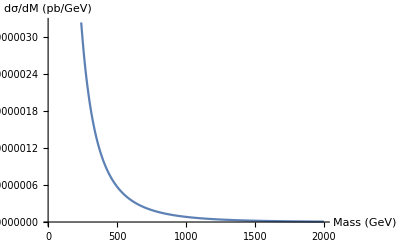

```mathematica
Plot[fint[x],{x,10,2000},AxesLabel->{"Mass (GeV)","dσ/dM (pb/GeV)"}]
```

```mathematica
F1=Integrate[fint[x],x]
```

InterpolatingFunction[…][x]

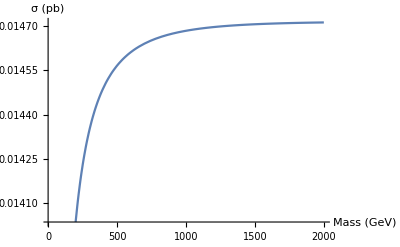

```mathematica
Plot[F1,{x,10,2000},AxesLabel->{"Mass (GeV)","σ (pb)"}]
```

```mathematica
F1n=Integrate[fint[x],{x,10,2000}]
```

0.0147123

```mathematica
fint[500]
```

5.74899×10^-7

```mathematica
F1[100]
```

InterpolatingFunction[…][x][100]

## Compare to Duhr Paper, (Npt = 50), 10 GeV < Mass < 2000 GeV, μ_F=100 GeV

```mathematica
Clear[data]
```

```mathematica
data1 = Import["~/Desktop/LegendreIntegration1.dat"]
```

{{10.,0.00190868,55.7115,5.91716×10^-7,0.0000342601,389379.},{49.8,0.0000820807,11.9311,0.0000146748,6.87954×10^-6,3152.72},{89.6,0.0000248123,6.48911,0.0000475039,3.82367×10^-6,541.314},{129.4,0.000011531,4.35524,0.0000990791,2.64761×10^-6,179.709},{169.2,6.5254×10^-6,3.22269,0.0001694,2.02483×10^-6,80.3844},{209.,4.13746×10^-6,2.52401,0.000258467,1.63924×10^-6,42.6515},{248.8,2.82538×10^-6,2.05182,0.000366281,1.37701×10^-6,25.2826},{288.6,2.03282×10^-6,1.71241,0.00049284,1.18711×10^-6,16.1988},{328.4,1.52037×10^-6,1.45735,0.000638145,1.04324×10^-6,10.9942},{368.2,1.17158×10^-6,1.25912,0.000802197,9.30476×10^-7,7.80048},{408.,9.24467×10^-7,1.10094,0.000984994,8.39709×10^-7,5.73314},{447.8,7.43658×10^-7,0.972005,0.00118654,7.65076×10^-7,4.33631},{487.6,6.0782×10^-7,0.865067,0.00140683,7.02628×10^-7,3.35878},{527.4,5.0349×10^-7,0.775073,0.00164586,6.49604×10^-7,2.65432},{567.2,4.21848×10^-7,0.698399,0.00190364,6.04022×10^-7,2.13385},{607.,3.56927×10^-7,0.632382,0.00218017,5.64417×10^-7,1.74103},{646.8,3.04581×10^-7,0.575021,0.00247545,5.29686×10^-7,1.43901},{686.6,2.61858×10^-7,0.524785,0.00278946,4.98982×10^-7,1.20299},{726.4,2.26615×10^-7,0.48048,0.00312223,4.71643×10^-7,1.01589},{766.2,1.97264×10^-7,0.441165,0.00347374,4.47143×10^-7,0.865658},{806.,1.72613×10^-7,0.406088,0.003844,4.25064×10^-7,0.743649},{845.8,1.51752×10^-7,0.374638,0.004233,4.05062×10^-7,0.643532},{885.6,1.33976×10^-7,0.346319,0.00464075,3.86858×10^-7,0.560609},{925.4,1.18736×10^-7,0.320718,0.00506725,3.7022×10^-7,0.491343},{965.2,1.05596×10^-7,0.297492,0.00551249,3.54954×10^-7,0.433033},{1005.,9.42082×10^-8,0.276354,0.00597648,3.40897×10^-7,0.383597},{1044.8,8.42928×10^-8,0.25706,0.00645921,3.27911×10^-7,0.341408},{1084.6,7.56221×10^-8,0.239403,0.00696069,3.15878×10^-7,0.305186},{1124.4,6.80097×10^-8,0.223205,0.00748092,3.04697×10^-7,0.273912},{1164.2,6.13021×10^-8,0.208312,0.00801989,2.9428×10^-7,0.246769},{1204.,5.53718×10^-8,0.194593,0.00857761,2.84552×10^-7,0.223097},{1243.8,5.01122×10^-8,0.18193,0.00915407,2.75447×10^-7,0.202358},{1283.6,4.5434×10^-8,0.170224,0.00974928,2.66907×10^-7,0.184113},{1323.4,4.12616×10^-8,0.159385,0.0103632,2.5888×10^-7,0.167996},{1363.2,3.75309×10^-8,0.149335,0.0109959,2.51321×10^-7,0.153707},{1403.,3.41875×10^-8,0.140002,0.0116474,2.44192×10^-7,0.140994},{1442.8,3.11844×10^-8,0.131327,0.0123176,2.37456×10^-7,0.129645},{1482.6,2.84815×10^-8,0.123253,0.0130065,2.31081×10^-7,0.119482},{1522.4,2.60441×10^-8,0.115731,0.0137142,2.2504×10^-7,0.110354},{1562.2,2.38421×10^-8,0.108716,0.0144406,2.19307×10^-7,0.102132},{1602.,2.18494×10^-8,0.102168,0.0151858,2.13858×10^-7,0.0947077},{1641.8,2.00433×10^-8,0.0960507,0.0159497,2.08674×10^-7,0.0879857},{1681.6,1.84038×10^-8,0.0903317,0.0167324,2.03735×10^-7,0.0818851},{1721.4,1.69133×10^-8,0.084981,0.0175338,1.99025×10^-7,0.0763357},{1761.2,1.55566×10^-8,0.0799713,0.018354,1.94527×10^-7,0.0712766},{1801.,1.432×10^-8,0.0752781,0.0191929,1.90228×10^-7,0.0666549},{1840.8,1.31916×10^-8,0.0708787,0.0200506,1.86115×10^-7,0.0624242},{1880.6,1.21607×10^-8,0.0667525,0.020927,1.82177×10^-7,0.0585442},{1920.4,1.12179×10^-8,0.0628805,0.0218221,1.78401×10^-7,0.0549791},{1960.2,1.03548×10^-8,0.0592453,0.022736,1.74779×10^-7,0.0516978},{2000.,9.56384×10^-9,0.0558308,0.0236686,1.71301×10^-7,0.0486724}}

```mathematica
TableForm[data1]
Mass1 = data1[[All,1]]
dσdM1 = data1[[All,2]]
```

10. | 0.00190868 | 55.7115 | 5.91716×10^-7 | 0.0000342601 | 389379.
49.8 | 0.0000820807 | 11.9311 | 0.0000146748 | 6.87954×10^-6 | 3152.72
89.6 | 0.0000248123 | 6.48911 | 0.0000475039 | 3.82367×10^-6 | 541.314
129.4 | 0.000011531 | 4.35524 | 0.0000990791 | 2.64761×10^-6 | 179.709
169.2 | 6.5254×10^-6 | 3.22269 | 0.0001694 | 2.02483×10^-6 | 80.3844
209. | 4.13746×10^-6 | 2.52401 | 0.000258467 | 1.63924×10^-6 | 42.6515
248.8 | 2.82538×10^-6 | 2.05182 | 0.000366281 | 1.37701×10^-6 | 25.2826
288.6 | 2.03282×10^-6 | 1.71241 | 0.00049284 | 1.18711×10^-6 | 16.1988
328.4 | 1.52037×10^-6 | 1.45735 | 0.000638145 | 1.04324×10^-6 | 10.9942
368.2 | 1.17158×10^-6 | 1.25912 | 0.000802197 | 9.30476×10^-7 | 7.80048
408. | 9.24467×10^-7 | 1.10094 | 0.000984994 | 8.39709×10^-7 | 5.73314
447.8 | 7.43658×10^-7 | 0.972005 | 0.00118654 | 7.65076×10^-7 | 4.33631
487.6 | 6.0782×10^-7 | 0.865067 | 0.00140683 | 7.02628×10^-7 | 3.35878
527.4 | 5.0349×10^-7 | 0.775073 | 0.00164586 | 6.49604×10^-7 | 2.65432
567.2 | 4.21848×10^-7 | 0.698399 | 0.00190364 | 6.04022×10^-7 | 2.13385
607. | 3.56927×10^-7 | 0.632382 | 0.00218017 | 5.64417×10^-7 | 1.74103
646.8 | 3.04581×10^-7 | 0.575021 | 0.00247545 | 5.29686×10^-7 | 1.43901
686.6 | 2.61858×10^-7 | 0.524785 | 0.00278946 | 4.98982×10^-7 | 1.20299
726.4 | 2.26615×10^-7 | 0.48048 | 0.00312223 | 4.71643×10^-7 | 1.01589
766.2 | 1.97264×10^-7 | 0.441165 | 0.00347374 | 4.47143×10^-7 | 0.865658
806. | 1.72613×10^-7 | 0.406088 | 0.003844 | 4.25064×10^-7 | 0.743649
845.8 | 1.51752×10^-7 | 0.374638 | 0.004233 | 4.05062×10^-7 | 0.643532
885.6 | 1.33976×10^-7 | 0.346319 | 0.00464075 | 3.86858×10^-7 | 0.560609
925.4 | 1.18736×10^-7 | 0.320718 | 0.00506725 | 3.7022×10^-7 | 0.491343
965.2 | 1.05596×10^-7 | 0.297492 | 0.00551249 | 3.54954×10^-7 | 0.433033
1005. | 9.42082×10^-8 | 0.276354 | 0.00597648 | 3.40897×10^-7 | 0.383597
1044.8 | 8.42928×10^-8 | 0.25706 | 0.00645921 | 3.27911×10^-7 | 0.341408
1084.6 | 7.56221×10^-8 | 0.239403 | 0.00696069 | 3.15878×10^-7 | 0.305186
1124.4 | 6.80097×10^-8 | 0.223205 | 0.00748092 | 3.04697×10^-7 | 0.273912
1164.2 | 6.13021×10^-8 | 0.208312 | 0.00801989 | 2.9428×10^-7 | 0.246769
1204. | 5.53718×10^-8 | 0.194593 | 0.00857761 | 2.84552×10^-7 | 0.223097
1243.8 | 5.01122×10^-8 | 0.18193 | 0.00915407 | 2.75447×10^-7 | 0.202358
1283.6 | 4.5434×10^-8 | 0.170224 | 0.00974928 | 2.66907×10^-7 | 0.184113
1323.4 | 4.12616×10^-8 | 0.159385 | 0.0103632 | 2.5888×10^-7 | 0.167996
1363.2 | 3.75309×10^-8 | 0.149335 | 0.0109959 | 2.51321×10^-7 | 0.153707
1403. | 3.41875×10^-8 | 0.140002 | 0.0116474 | 2.44192×10^-7 | 0.140994
1442.8 | 3.11844×10^-8 | 0.131327 | 0.0123176 | 2.37456×10^-7 | 0.129645
1482.6 | 2.84815×10^-8 | 0.123253 | 0.0130065 | 2.31081×10^-7 | 0.119482
1522.4 | 2.60441×10^-8 | 0.115731 | 0.0137142 | 2.2504×10^-7 | 0.110354
1562.2 | 2.38421×10^-8 | 0.108716 | 0.0144406 | 2.19307×10^-7 | 0.102132
1602. | 2.18494×10^-8 | 0.102168 | 0.0151858 | 2.13858×10^-7 | 0.0947077
1641.8 | 2.00433×10^-8 | 0.0960507 | 0.0159497 | 2.08674×10^-7 | 0.0879857
1681.6 | 1.84038×10^-8 | 0.0903317 | 0.0167324 | 2.03735×10^-7 | 0.0818851
1721.4 | 1.69133×10^-8 | 0.084981 | 0.0175338 | 1.99025×10^-7 | 0.0763357
1761.2 | 1.55566×10^-8 | 0.0799713 | 0.018354 | 1.94527×10^-7 | 0.0712766
1801. | 1.432×10^-8 | 0.0752781 | 0.0191929 | 1.90228×10^-7 | 0.0666549
1840.8 | 1.31916×10^-8 | 0.0708787 | 0.0200506 | 1.86115×10^-7 | 0.0624242
1880.6 | 1.21607×10^-8 | 0.0667525 | 0.020927 | 1.82177×10^-7 | 0.0585442
1920.4 | 1.12179×10^-8 | 0.0628805 | 0.0218221 | 1.78401×10^-7 | 0.0549791
1960.2 | 1.03548×10^-8 | 0.0592453 | 0.022736 | 1.74779×10^-7 | 0.0516978
2000. | 9.56384×10^-9 | 0.0558308 | 0.0236686 | 1.71301×10^-7 | 0.0486724

{10.,49.8,89.6,129.4,169.2,209.,248.8,288.6,328.4,368.2,408.,447.8,487.6,527.4,567.2,607.,646.8,686.6,726.4,766.2,806.,845.8,885.6,925.4,965.2,1005.,1044.8,1084.6,1124.4,1164.2,1204.,1243.8,1283.6,1323.4,1363.2,1403.,1442.8,1482.6,1522.4,1562.2,1602.,1641.8,1681.6,1721.4,1761.2,1801.,1840.8,1880.6,1920.4,1960.2,2000.}

{0.00190868,0.0000820807,0.0000248123,0.000011531,6.5254×10^-6,4.13746×10^-6,2.82538×10^-6,2.03282×10^-6,1.52037×10^-6,1.17158×10^-6,9.24467×10^-7,7.43658×10^-7,6.0782×10^-7,5.0349×10^-7,4.21848×10^-7,3.56927×10^-7,3.04581×10^-7,2.61858×10^-7,2.26615×10^-7,1.97264×10^-7,1.72613×10^-7,1.51752×10^-7,1.33976×10^-7,1.18736×10^-7,1.05596×10^-7,9.42082×10^-8,8.42928×10^-8,7.56221×10^-8,6.80097×10^-8,6.13021×10^-8,5.53718×10^-8,5.01122×10^-8,4.5434×10^-8,4.12616×10^-8,3.75309×10^-8,3.41875×10^-8,3.11844×10^-8,2.84815×10^-8,2.60441×10^-8,2.38421×10^-8,2.18494×10^-8,2.00433×10^-8,1.84038×10^-8,1.69133×10^-8,1.55566×10^-8,1.432×10^-8,1.31916×10^-8,1.21607×10^-8,1.12179×10^-8,1.03548×10^-8,9.56384×10^-9}

```mathematica
fint1 = Interpolation[Transpose[{Mass1,dσdM1}],InterpolationOrder->3]
```

InterpolatingFunction[…]

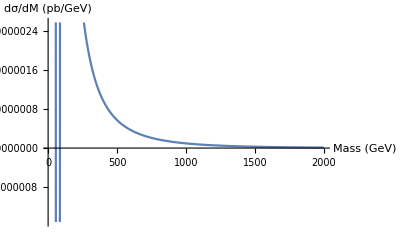

```mathematica
Plot[fint1[x],{x,10,2000},AxesLabel->{"Mass (GeV)","dσ/dM (pb/GeV)"}]
```

```mathematica
F1=Integrate[fint1[x],x]
```

InterpolatingFunction[…][x]

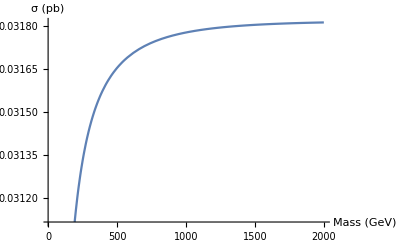

```mathematica
Plot[F1,{x,10,2000},AxesLabel->{"Mass (GeV)","σ (pb)"}]
```

```mathematica
F1n1=Integrate[fint1[x],{x,10,100}]
```

0.0302299

## Compare to Dr. Guzzi

```mathematica
dataGuz = Import["~/Desktop/QFT/GnuplotPractice/compareGuz.dat"];
```

```mathematica
TableForm[dataGuz]
Q = dataGuz[[All,1]]
dσDQ = dataGuz[[All,2]]
```

100 | 0.000192191
106 | 0.000151694
112 | 0.000121161
118 | 0.0000978155
124 | 0.0000797394
130 | 0.000065576
136 | 0.0000543614
142 | 0.0000453979
148 | 0.0000381702
154 | 0.0000322938
160 | 0.000027481
166 | 0.0000235117
172 | 0.0000202162
178 | 0.0000174636
184 | 0.0000151516
190 | 0.0000131998
196 | 0.000011544
202 | 0.0000101325
208 | 8.92416×10^-6
214 | 7.88517×10^-6
220 | 6.98829×10^-6
226 | 6.21122×10^-6
232 | 5.53562×10^-6
238 | 4.94638×10^-6
244 | 4.4309×10^-6
250 | 3.97851×10^-6
256 | 3.58035×10^-6
262 | 3.22892×10^-6
268 | 2.91791×10^-6
274 | 2.64197×10^-6
280 | 2.39659×10^-6
286 | 2.17791×10^-6
292 | 1.98264×10^-6
298 | 1.80789×10^-6
304 | 1.65117×10^-6
310 | 1.51036×10^-6
316 | 1.38357×10^-6
322 | 1.26919×10^-6
328 | 1.16582×10^-6
334 | 1.07227×10^-6
340 | 9.87476×10^-7
346 | 9.10516×10^-7
352 | 8.40557×10^-7
358 | 7.76862×10^-7
364 | 7.18784×10^-7
370 | 6.65744×10^-7
376 | 6.17238×10^-7
382 | 5.72823×10^-7
388 | 5.32114×10^-7
394 | 4.94767×10^-7
400 | 4.60467×10^-7
406 | 4.28929×10^-7
412 | 3.99899×10^-7
418 | 3.73144×10^-7
424 | 3.48456×10^-7
430 | 3.25649×10^-7
436 | 3.04562×10^-7
442 | 2.85048×10^-7
448 | 2.66978×10^-7
454 | 2.50233×10^-7
460 | 2.34704×10^-7
466 | 2.20288×10^-7
472 | 2.06895×10^-7
478 | 1.94437×10^-7
484 | 1.82837×10^-7
490 | 1.72028×10^-7
496 | 1.61947×10^-7
502 | 1.52541×10^-7
508 | 1.4376×10^-7
514 | 1.35559×10^-7
520 | 1.27896×10^-7
526 | 1.20732×10^-7
532 | 1.14029×10^-7
538 | 1.07753×10^-7
544 | 1.01871×10^-7
550 | 9.63542×10^-8
556 | 9.11754×10^-8
562 | 8.6311×10^-8
568 | 8.17403×10^-8
574 | 7.74441×10^-8
580 | 7.34049×10^-8
586 | 6.9606×10^-8
592 | 6.60319×10^-8
598 | 6.26678×10^-8
604 | 5.95×10^-8
610 | 5.65154×10^-8
616 | 5.37015×10^-8
622 | 5.10468×10^-8
628 | 4.85403×10^-8
634 | 4.61721×10^-8
640 | 4.39331×10^-8
646 | 4.18153×10^-8
652 | 3.98114×10^-8
658 | 3.79147×10^-8
664 | 3.6119×10^-8
670 | 3.44186×10^-8
676 | 3.28082×10^-8
682 | 3.12826×10^-8
688 | 2.98371×10^-8
694 | 2.84672×10^-8
700 | 2.71685×10^-8

{100,106,112,118,124,130,136,142,148,154,160,166,172,178,184,190,196,202,208,214,220,226,232,238,244,250,256,262,268,274,280,286,292,298,304,310,316,322,328,334,340,346,352,358,364,370,376,382,388,394,400,406,412,418,424,430,436,442,448,454,460,466,472,478,484,490,496,502,508,514,520,526,532,538,544,550,556,562,568,574,580,586,592,598,604,610,616,622,628,634,640,646,652,658,664,670,676,682,688,694,700}

{0.000192191,0.000151694,0.000121161,0.0000978155,0.0000797394,0.000065576,0.0000543614,0.0000453979,0.0000381702,0.0000322938,0.000027481,0.0000235117,0.0000202162,0.0000174636,0.0000151516,0.0000131998,0.000011544,0.0000101325,8.92416×10^-6,7.88517×10^-6,6.98829×10^-6,6.21122×10^-6,5.53562×10^-6,4.94638×10^-6,4.4309×10^-6,3.97851×10^-6,3.58035×10^-6,3.22892×10^-6,2.91791×10^-6,2.64197×10^-6,2.39659×10^-6,2.17791×10^-6,1.98264×10^-6,1.80789×10^-6,1.65117×10^-6,1.51036×10^-6,1.38357×10^-6,1.26919×10^-6,1.16582×10^-6,1.07227×10^-6,9.87476×10^-7,9.10516×10^-7,8.40557×10^-7,7.76862×10^-7,7.18784×10^-7,6.65744×10^-7,6.17238×10^-7,5.72823×10^-7,5.32114×10^-7,4.94767×10^-7,4.60467×10^-7,4.28929×10^-7,3.99899×10^-7,3.73144×10^-7,3.48456×10^-7,3.25649×10^-7,3.04562×10^-7,2.85048×10^-7,2.66978×10^-7,2.50233×10^-7,2.34704×10^-7,2.20288×10^-7,2.06895×10^-7,1.94437×10^-7,1.82837×10^-7,1.72028×10^-7,1.61947×10^-7,1.52541×10^-7,1.4376×10^-7,1.35559×10^-7,1.27896×10^-7,1.20732×10^-7,1.14029×10^-7,1.07753×10^-7,1.01871×10^-7,9.63542×10^-8,9.11754×10^-8,8.6311×10^-8,8.17403×10^-8,7.74441×10^-8,7.34049×10^-8,6.9606×10^-8,6.60319×10^-8,6.26678×10^-8,5.95×10^-8,5.65154×10^-8,5.37015×10^-8,5.10468×10^-8,4.85403×10^-8,4.61721×10^-8,4.39331×10^-8,4.18153×10^-8,3.98114×10^-8,3.79147×10^-8,3.6119×10^-8,3.44186×10^-8,3.28082×10^-8,3.12826×10^-8,2.98371×10^-8,2.84672×10^-8,2.71685×10^-8}

```mathematica
fintGuz = Interpolation[Transpose[{Q,dσDQ}],InterpolationOrder->3]
```

InterpolatingFunction[…]

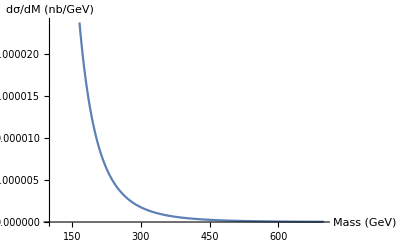

```mathematica
Plot[fintGuz[x],{x,100,700},AxesLabel->{"Mass (GeV)","dσ/dM (nb/GeV)"}]
```

```mathematica
F1Guz=Integrate[fintGuz[x],x]
```

InterpolatingFunction[…][x]

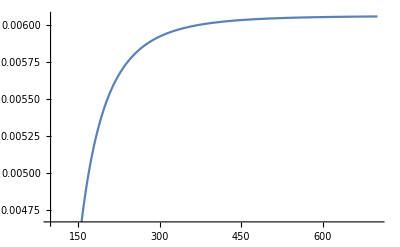

```mathematica
Plot[F1Guz,{x,100,700}]
```

InterpolatingFunction::dmval: Input value {10.0407} lies outside the range of data in the interpolating function. Extrapolation will be used.

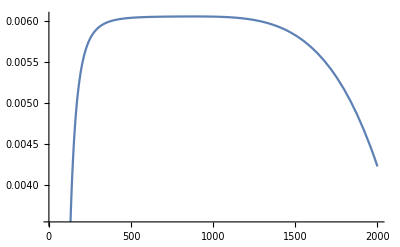

```mathematica
Plot[F1Guz,{x,10,2000}]
```

## Scratch 1

```mathematica
data1 = Import["~/Desktop/LegendreIntegration10_2000.dat"]
```

{{10.,0.0014476,12.2509,2.04082×10^-6,0.000118162,389379.},{109.5,0.0000283664,2.62869,0.000244699,0.0000107911,296.572},{209.,6.79718×10^-6,1.20225,0.000891449,5.65371×10^-6,42.6515},{308.5,2.61661×10^-6,0.683148,0.00194229,3.83023×10^-6,13.262},{408.,1.24185×10^-6,0.428796,0.00339722,2.89614×10^-6,5.73314},{507.5,6.62485×10^-7,0.284533,0.00525625,2.32832×10^-6,2.97896},{607.,3.80438×10^-7,0.195431,0.00751937,1.94666×10^-6,1.74103},{706.5,2.29685×10^-7,0.13733,0.0101866,1.6725×10^-6,1.10417},{806.,1.43725×10^-7,0.0980364,0.0132579,1.46604×10^-6,0.743649},{905.5,9.23573×10^-8,0.070775,0.0167333,1.30494×10^-6,0.524454},{1005.,6.05627×10^-8,0.05151,0.0206128,1.17575×10^-6,0.383597},{1104.5,4.03428×10^-8,0.0377097,0.0248963,1.06983×10^-6,0.288985},{1204.,2.72079×10^-8,0.0277231,0.029584,9.81416×10^-7,0.223097},{1303.5,1.85298×10^-8,0.020441,0.0346758,9.06501×10^-7,0.175808},{1403.,1.27176×10^-8,0.0151003,0.0401716,8.42213×10^-7,0.140994},{1502.5,8.78182×10^-9,0.0111666,0.0460716,7.86439×10^-7,0.114797},{1602.,6.09267×10^-9,0.0082602,0.0523756,7.37593×10^-7,0.0947077},{1701.5,4.24199×10^-9,0.00610832,0.0590837,6.94461×10^-7,0.0790455},{1801.,2.96097×10^-9,0.00451303,0.0661959,6.56094×10^-7,0.0666549},{1900.5,2.07023×10^-9,0.00332972,0.0737123,6.21744×10^-7,0.0567243},{2000.,1.44872×10^-9,0.00245209,0.0816327,5.90812×10^-7,0.0486724}}

```mathematica
TableForm[data1]
```

10. | 0.0014476 | 12.2509 | 2.04082×10^-6 | 0.000118162 | 389379.
109.5 | 0.0000283664 | 2.62869 | 0.000244699 | 0.0000107911 | 296.572
209. | 6.79718×10^-6 | 1.20225 | 0.000891449 | 5.65371×10^-6 | 42.6515
308.5 | 2.61661×10^-6 | 0.683148 | 0.00194229 | 3.83023×10^-6 | 13.262
408. | 1.24185×10^-6 | 0.428796 | 0.00339722 | 2.89614×10^-6 | 5.73314
507.5 | 6.62485×10^-7 | 0.284533 | 0.00525625 | 2.32832×10^-6 | 2.97896
607. | 3.80438×10^-7 | 0.195431 | 0.00751937 | 1.94666×10^-6 | 1.74103
706.5 | 2.29685×10^-7 | 0.13733 | 0.0101866 | 1.6725×10^-6 | 1.10417
806. | 1.43725×10^-7 | 0.0980364 | 0.0132579 | 1.46604×10^-6 | 0.743649
905.5 | 9.23573×10^-8 | 0.070775 | 0.0167333 | 1.30494×10^-6 | 0.524454
1005. | 6.05627×10^-8 | 0.05151 | 0.0206128 | 1.17575×10^-6 | 0.383597
1104.5 | 4.03428×10^-8 | 0.0377097 | 0.0248963 | 1.06983×10^-6 | 0.288985
1204. | 2.72079×10^-8 | 0.0277231 | 0.029584 | 9.81416×10^-7 | 0.223097
1303.5 | 1.85298×10^-8 | 0.020441 | 0.0346758 | 9.06501×10^-7 | 0.175808
1403. | 1.27176×10^-8 | 0.0151003 | 0.0401716 | 8.42213×10^-7 | 0.140994
1502.5 | 8.78182×10^-9 | 0.0111666 | 0.0460716 | 7.86439×10^-7 | 0.114797
1602. | 6.09267×10^-9 | 0.0082602 | 0.0523756 | 7.37593×10^-7 | 0.0947077
1701.5 | 4.24199×10^-9 | 0.00610832 | 0.0590837 | 6.94461×10^-7 | 0.0790455
1801. | 2.96097×10^-9 | 0.00451303 | 0.0661959 | 6.56094×10^-7 | 0.0666549
1900.5 | 2.07023×10^-9 | 0.00332972 | 0.0737123 | 6.21744×10^-7 | 0.0567243
2000. | 1.44872×10^-9 | 0.00245209 | 0.0816327 | 5.90812×10^-7 | 0.0486724

```mathematica
f2=Interpolation[{{10.0,0.0014476016522},{109.5,0.000028366417058},{209.0,6.7971822877*^-6},{308.5,2.6166101783*^-6},{408.0,1.2418517362*^-6},{507.5,6.6248501814*^-7},{607.0,3.8043799*^-7},{706.5,2.2968530692*^-7},{806.0,1.4372482436*^-7},{905.5,9.2357284337*^-8},{1005.0,6.0562660304*^-8},{1104.5,4.0342834842*^-8},{1204.0,2.7207857285*^-8},{1303.5,1.8529763079*^-8},{1403.0,1.271763418*^-8},{1502.5,8.7818193897*^-9},{1602.0,6.0926683905*^-9},{1701.5,4.241990071*^-9},{1801.0,2.9609696807*^-9},{1900.5,2.0702320905*^-9},{2000.0,1.4487247078*^-9}}]
```

InterpolatingFunction[…]

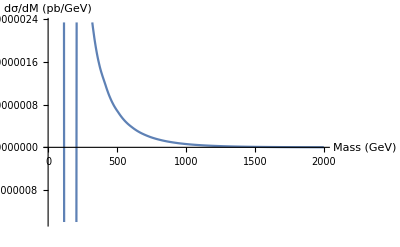

```mathematica
Plot[f2[x],{x,10,2000},AxesLabel->{"Mass (GeV)","dσ/dM (pb/GeV)"}]
```

```mathematica
F2=Integrate[f2[x],{x,10.0,2000.0}]
```

0.0527846

```mathematica
7000*7000
```

49000000

```mathematica
N[(10*10)/49000000]
```

2.04082×10^-6

```mathematica
F2i =Integrate[f2[x],x]
```

InterpolatingFunction[…][x]

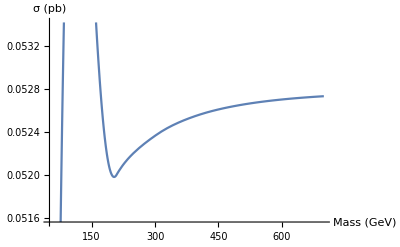

```mathematica
Plot[F2i,{x,50,700},AxesLabel->{"Mass (GeV)","σ (pb)"}]
```

## Scratch 2

```mathematica
data = Import["~/Desktop/LegendreIntegration.dat"]
```

{{100.,0.0000342197,2.89599,0.000204082,0.0000118162,389.379},{160.,0.0000125257,1.69607,0.000522449,7.38515×10^-6,95.0633},{220.,6.02184×10^-6,1.12117,0.000987755,5.37102×10^-6,36.5683},{280.,3.34542×10^-6,0.792738,0.0016,4.22009×10^-6,17.7378},{340.,2.03246×10^-6,0.584819,0.00235918,3.47537×10^-6,9.90686},{400.,1.31182×10^-6,0.444073,0.00326531,2.95406×10^-6,6.08405},{460.,8.84276×10^-7,0.344244,0.00431837,2.56875×10^-6,4.00036},{520.,6.15776×10^-7,0.270986,0.00551837,2.27235×10^-6,2.76925},{580.,4.39712×10^-7,0.215833,0.00686531,2.03728×10^-6,1.99567},{640.,3.20299×10^-7,0.173482,0.00835918,1.84629×10^-6,1.48536},{700.,2.37095×10^-7,0.140456,0.01,1.68804×10^-6,1.13522}}

```mathematica
TableForm[data]
```

100. | 0.0000342197 | 2.89599 | 0.000204082 | 0.0000118162 | 389.379
160. | 0.0000125257 | 1.69607 | 0.000522449 | 7.38515×10^-6 | 95.0633
220. | 6.02184×10^-6 | 1.12117 | 0.000987755 | 5.37102×10^-6 | 36.5683
280. | 3.34542×10^-6 | 0.792738 | 0.0016 | 4.22009×10^-6 | 17.7378
340. | 2.03246×10^-6 | 0.584819 | 0.00235918 | 3.47537×10^-6 | 9.90686
400. | 1.31182×10^-6 | 0.444073 | 0.00326531 | 2.95406×10^-6 | 6.08405
460. | 8.84276×10^-7 | 0.344244 | 0.00431837 | 2.56875×10^-6 | 4.00036
520. | 6.15776×10^-7 | 0.270986 | 0.00551837 | 2.27235×10^-6 | 2.76925
580. | 4.39712×10^-7 | 0.215833 | 0.00686531 | 2.03728×10^-6 | 1.99567
640. | 3.20299×10^-7 | 0.173482 | 0.00835918 | 1.84629×10^-6 | 1.48536
700. | 2.37095×10^-7 | 0.140456 | 0.01 | 1.68804×10^-6 | 1.13522

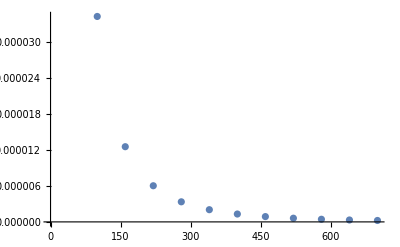

```mathematica
ListPlot[data[[All,1;;2]]]
```

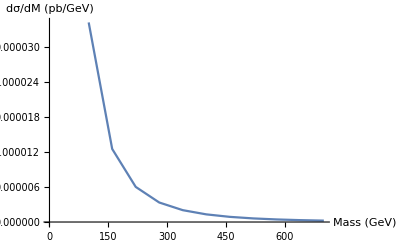

```mathematica
ListPlot[data[[All,1;;2]], Joined ->True,AxesLabel->{"Mass (GeV)","dσ/dM (pb/GeV)"}]
```

```mathematica
Col1 = data[[All,1]]
Col2 = data[[All,2]]
```

{100.,160.,220.,280.,340.,400.,460.,520.,580.,640.,700.}

{0.0000342197,0.0000125257,6.02184×10^-6,3.34542×10^-6,2.03246×10^-6,1.31182×10^-6,8.84276×10^-7,6.15776×10^-7,4.39712×10^-7,3.20299×10^-7,2.37095×10^-7}

```mathematica
f1=Interpolation[{{100,0.000034219707734000005},{160,0.000012525731706000002},{220,6.0218421652*^-6},{280,3.3454241719*^-6},{340,2.0324602065*^-6},{400,1.3118182065999999*^-6},{460,8.842761748399998*^-7},{520,6.157761619699999*^-7},{580,4.3971206647*^-7},{640,3.2029866579*^-7},{700,2.3709471682999998*^-7}}]
```

InterpolatingFunction[…]

```mathematica
Plot[f1[x],{x,100,700},AxesLabel->{"Mass (GeV)","dσ/dM (pb/GeV)"}]
```

-Graphics-

```mathematica
F1=Integrate[f1[x],x]
```

InterpolatingFunction[…][x]

```mathematica
Plot[F1,{x,50,700},AxesLabel->{"Mass (GeV)","σ (pb)"}]
```

InterpolatingFunction::dmval: Input value {50.0133} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
fint = Interpolation[Transpose[{Col1,Col2}],InterpolationOrder->3]
```

InterpolatingFunction[…]

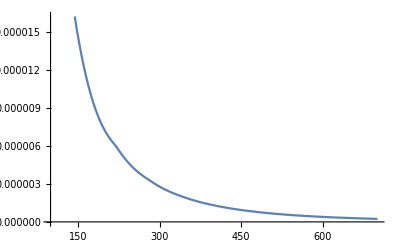

```mathematica
Plot[%[x],{x,100,700}]
```

```mathematica
(100)^2/(13000)^2
```

1/16900

```mathematica
N[1/16900]
```

0.0000591716

```mathematica
MatA={{dx,0,0},{0,dy,0},{0,0,dz}}
MatB = {{a},{b},{c}}
```

{{dx,0,0},{0,dy,0},{0,0,dz}}

{{a},{b},{c}}

```mathematica
MatA.MatA//MatrixForm
```

(dx^2 | 0 | 0
0 | dy^2 | 0
0 | 0 | dz^2)

```mathematica
MatA.%//MatrixForm
```

(a dx^2
b dy^2
c dz^2)

```mathematica
Transpose[MatB].(MatA)
```

{{a dx,b dy,c dz}}

```mathematica
MatA={{dx,0,0},{0,dy,0},{0,0,dz}}
MatB = {{dx,0,0},{0,dy,0},{0,0,dz}}
MatG = {{-1,0,0},{0,1,0},{0,0,1}}
MatA.MatB.MatG //MatrixForm
```

{{dx,0,0},{0,dy,0},{0,0,dz}}

{{dx,0,0},{0,dy,0},{0,0,dz}}

{{-1,0,0},{0,1,0},{0,0,1}}

(-dx^2 | 0 | 0
0 | dy^2 | 0
0 | 0 | dz^2)